```mathematica
"SINGLE CSTR";

Clear[k1,k2,k3,Cao]
Solve[Ca-Cao==t*(-k1*Ca-k3*Ca^2),Ca]
Solve[Cb==t*(Ca-k2*Cb),Cb]
Solve[Cc==t*k2*Cb,Cc]
Solve[Cd==t*k3*Ca^2,Cd]
```

{{Ca→(-1-k1 t-√(4 Cao k3 t+(1+k1 t)^2))/(2 k3 t)},{Ca→(-1-k1 t+√(4 Cao k3 t+(1+k1 t)^2))/(2 k3 t)}}

{{Cb→(Ca t)/(1+k2 t)}}

{{Cc→Cb k2 t}}

{{Cd→Ca^2 k3 t}}

```mathematica
Solve[Ca2-Ca== 2*t*(-k1*Ca2-k3*Ca2^2),Ca2]
Solve[Cb2-Cb==2* t*(Ca2-k2*Cb2),Cb2]
Solve[Cc2-Cc==2* t*k2*Cb2,Cc2]
Solve[Cd2-Cd== 2*t*k3*Ca2^2,Cd2]
```

{{Ca2→(-1-2 k1 t-√(8 Ca k3 t+(1+2 k1 t)^2))/(4 k3 t)},{Ca2→(-1-2 k1 t+√(8 Ca k3 t+(1+2 k1 t)^2))/(4 k3 t)}}

{{Cb2→(Cb+2 Ca2 t)/(1+2 k2 t)}}

{{Cc2→Cc+2 Cb2 k2 t}}

{{Cd2→Cd+2 Ca2^2 k3 t}}

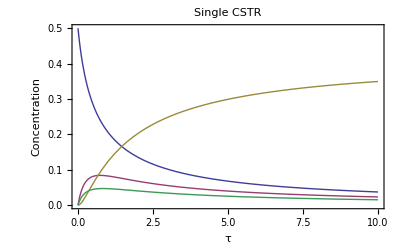

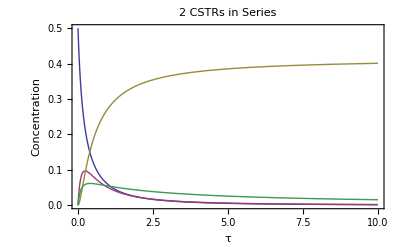

Single CSTR Information

{0.0841698 p-xylene,{p-xylene (t→0.737584)}}

0.24037 m-xylene

0.0931235 o-xylene

0.0468777 d

CSTRs in Series Information

{0.0968018 p-xylene,{p-xylene (t→0.23796)}}

0.215132 m-xylene

0.091778 o-xylene

0.0585727 d

```mathematica
k1=1.2;
k2=1.5;
k3=1.1;
Cao=0.5;
CaCSTR[t_]=(-1-k1*t+√(4*Cao*k3*t+(1+k1*t)^2))/(2*k3*t);
CbCSTR[t_]=(t*CaCSTR[t])/(1+k2*t);
CcCSTR[t_]=CbCSTR[t]*k2*t;
CdCSTR[t_]=(CaCSTR[t]^2)*k3*t;

CaCSTRseries[t_]=(-1-2*k1*t+√(8*CaCSTR[t]*k3*t+(1+2*k1*t)^2))/(4*k3*t);
CbCSTRseries[t_]=(CbCSTR[t]+2*CaCSTRseries[t]*t)/(1+2*k2*t);
CcCSTRseries[t_]=2*t*k2*CbCSTRseries[t]+CcCSTR[t];
CdCSTRseries[t_]=CdCSTR[t]+2*k3*t*CaCSTRseries[t]^2;

Needs["PlotLegends`"];

Plot[{CaCSTR[t],CbCSTR[t],CcCSTR[t], CdCSTR[t]},{t,0,10},PlotRange->All,PlotLegend->{"m-xylene", "p-xylene", "o-xylene", "d"}, LegendPosition->{1.1,-0.4}, Frame->True, PlotStyle->{Thick}, PlotLabel->Style["Single CSTR",16],FrameLabel->{"τ","Concentration"}]

Plot[{CaCSTRseries[t],CbCSTRseries[t],CcCSTRseries[t],CdCSTRseries[t]},{t,0,10}, PlotRange->All, PlotLegend->{"m-xylene", "p-xylene", "o-xylene", "d"}, LegendPosition->{1.1,-0.4}, Frame->True, PlotStyle->{Thick}, PlotLabel->Style["2 CSTRs in Series",16],FrameLabel->{"τ","Concentration"}]

"Single CSTR Information"
"p-xylene"FindMaximum[CbCSTR[t],{t,0.1}]
"m-xylene" CaCSTR[0.737584]
"o-xylene" CcCSTR[0.737584]
"d" CdCSTR[0.737584]

"CSTRs in Series Information"
"p-xylene"FindMaximum[CbCSTRseries[t],{t,0.1}]
"m-xylene" CaCSTRseries[0.23795964192427874]
"o-xylene" CcCSTRseries[0.23795964192427874]
"d" CdCSTRseries[0.23795964192427874]
```